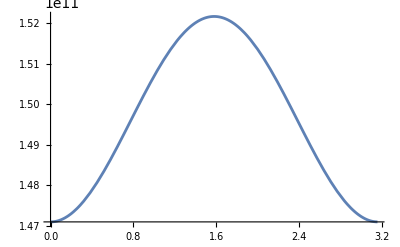

```mathematica
vi=30290;
ri=1.471*10^11;
vang=vi/ri;
c=ri^2*vang;
G=6.6743*10^-11;
mterra=5.97219*10^24;
msole=1*(1.98847*10^30);
sol=Simplify[NDSolve[{mterra*(r''[t]-c^2/r[t]^3)==-(G*(mterra*msole/r[t]^2)),r'[0]==0, r[0]== ri},{r[t]},{t,0,31.536*10^6}]]//Flatten;
rf[t_]=r[t]/. sol;

Plot[rf[t],{t,0,31.536*10^6}]
```